To load the functionality for certifying operator identities via noncommutative Groebner basis computations, just load the OperatorGB package. This can be done by the following command, provided that the file OperatorGB.m and this file are located in the same directory:

```mathematica
SetDirectory[NotebookDirectory[]];
<<OperatorGB.m
```

Package OperatorGB version 1.4.2
Copyright 2019, Institute of Mathematics, University of Kassel
by Clemens Hofstadler, clemens.hofstadler@mathematik.uni-kassel.de

We note that this documentation should be understandable without further theoretical knowledge; at least the first section, which shall be the standard use-case of this package. For the theory behind this package and further information/details we refer to this paper as well as this thesis.

## Certifying operator identities

In this section, we describe the standard use-case of this package, which is to automatically prove operator identities.

We illustrate the functionality of the package and its usage on a concrete example. To this end, we assume that we are given two linear operators A:V → W and B:U→ V, together with inner inverses, denoted by A^- and B^-, respectively, i.e. operators satisfying A A^-A=A and B B^-B=B.

We want to prove that B^-A^- is an inner inverse of A B, i.e. that

							 A B B^-A^-A B = A B
							
holds, provided that the operator A^-A B B^- is idempotent. This means A^-A B B^- A^-A B B^- = A^-A B B^-.

To prove such an operator identity, first, all equations involved have to be translated into (noncommutative) polynomials. This can be done by uniformly replacing each operator by an indeterminate and forming the differences of the left and right hand side of each operator identity. Note that this also includes the identity operator. Then, also the properties of composition of the identity with other operators have to be added to the assumptions.

In our example, we replace A by a, B by b, A^- by a^- and  B^-by b^-.  Additionally, we also collect all our assumptions in a set named “assumptions”.  Also, note that we have to use Mathematica’s noncommutative multiplication to obtain noncommutative polynomials.

```mathematica
assumptions = {a**SuperMinus[a]**a-a,b**SuperMinus[b]**b-b,SuperMinus[a]**a**b**SuperMinus[b]**SuperMinus[a]**a**b**SuperMinus[b]-SuperMinus[a]**a**b**SuperMinus[b]};
claim = a**b**SuperMinus[b]**SuperMinus[a]**a**b-a**b;
```

We also have to construct a labelled quiver, which is a labelled directed multigraph. This quiver shall relate the indeterminates with the domains and codomains of the corresponding operators.

Such a quiver can be defined by providing a list of triples. For every operator L appearing in our operator identities, we have to provide a triple of the form {l,s,t}, where l is the name of the indeterminate that we have replaced L with, s is the codomain of L and t the domain of L. Hence, we can set up a quiver Q for our example as follows:

```mathematica
Q={{a,V,W},{SuperMinus[a],W,V},{b,U,V},{SuperMinus[b],V,U}};
```

Now, we can call the method “Certify”, which takes a set of assumptions, a claim (all in form of noncommutative polynomials) and a quiver Q as input and returns either a linear combination of the claim in terms of the assumptions, which proves that the  corresponding claimed operator identity is indeed a consequence of the assumed identities, or $Failed, which indicates that the program was not able to prove that the claimed identity follows from the assumptions.

```mathematica
Certify[assumptions,claim,Q]
```

Done! All claims were successfully reduced to 0.

{{a,-b+b**b^-**b,1},{-a**b**b^-**a^-**a,-b+b**b^-**b,1},{a,-a^-**a**b**b^-+a^-**a**b**b^-**a^-**a**b**b^-,b},{-1,-a+a**a^-**a,b**b^-**a^-**a**b**b^-**b},{1,-a+a**a^-**a,b**b^-**b}}

In case of our example, we obtain a linear combination of the claim in terms of the assumptions in form of a list of triples. In other words, we get {{ a_1, f_1, b_1 },... ,{ a_n, f_n, b_n }} such that 
						claim = ∑_(i=1)^n a_i f_i b_i
and f_i∈ assumptions for 1 ≤ i ≤ n.

This linear combination serves as a certificate that the claimed operator identity is indeed a consequence of the assumed identities. We can also expand this linear combination and check that it indeed equals the claim.

```mathematica
MultiplyOut[%] === claim
```

True

## Certifying ideal membership

In this section, we discuss the algebraic computations done during the execution of the “Certify” command. To this end, we assume that the reader has a basic knowledge about Groebner bases in the free algebra.

From an algebraic point of view, verifying that a claimed operator identity is a consequence of certain assumptions, corresponds to showing the ideal membership of the (noncommutative) polynomial corresponding to this claim in the ideal generated by the polynomials corresponding to the assumptions. Although the ideal membership problem of noncommutative polynomials is undecidable in general, in practice it can often be solved with (partial) Groebner bases. Therefore, this package also provides functionality to compute (partial) Groebner bases in the free algebra.

To be able to compute (partial) Groebner bases of noncommutative polynomial ideals, the user first has to set up a corresponding noncommutative polynomial ring. This is done by providing a list of all indeterminates that the ring shall contain. In the following, we set up a noncommutative polynomial ring in the indeterminates  a, b, a^-, b^-.

```mathematica
SetUpRing[{a,SuperMinus[a],b,SuperMinus[b]}]
```

The monomial order in this polynomial ring is predefined to be degree lexicographic, where the indeterminates are ordered in ascending order corresponding to the input list of the “SetUpRing” method. Hence, in our case, we get  a < b < a^- < b^-.

The user has the option to change the monomial order. The second pre-defined order is a weighted degree lexicographic order. To switch to this order, the user has to execute the following command:

```mathematica
SortedQ = WeightedDegLex;
```

Then, additionally, a list of weights  {w_1, w_2,... } named “Weight” has to be provided, where w_1 corresponds to the weight of the first indeterminate in the input list of “SetUpRing”, w_2 to the second one and so on. For our example, we could set

```mathematica
Weight = {5,5,1,3};
```

Then a and b are weighted with a factor of 5,  a^- with a factor of 1 and b^- with a factor of 3.

Additionally, it is also possible to define a multigraded lexicographic order. This can be done by calling “SetUpRing” with two lists instead of one. For example,

```mathematica
SetUpRing[{a,SuperMinus[a]},{b,SuperMinus[b]}]
```

would given a block order consisting of two blocks; the first block of indeterminates being  a and   a^- and the second block  b and b^-, respectively.

To define an individual order, the user can also provide a binary function SortedQ[w,w'] acting on the set of all words that can be formed over the alphabet of indeterminates. It decides, when given two words w and w' as input, which of them is larger, by returning True if w ≤ w' and False otherwise. Note that for the function “SortedQ” a word w = x_i_1 x_i_2... x_i_nhas to be provided in form of a list {x_i_1, x_i_2,..., x_i_n}.

For now, however, we will stick to the degree lexicographic order.

```mathematica
SortedQ = DegLex;
```

An ideal in this polynomial ring can be defined simply by providing the generators as polynomials using Mathematica’s built in noncommutative multiplication. As an example, we consider the ideal generated by the polynomials that we also used in the previous section.

```mathematica
ideal = {a**SuperMinus[a]**a-a,b**SuperMinus[b]**b-b,SuperMinus[a]**a**b**SuperMinus[b]**SuperMinus[a]**a**b**SuperMinus[b]-SuperMinus[a]**a**b**SuperMinus[b]};
```

To now compute a Groebner basis of this ideal, we can call the method “Groebner”. Besides an ideal, this method takes an additional parameter (in this example named “cofactorsG”), which can basically be an arbitrary name and is not of importance for us now. For more information on this parameter please see the subsection “Additional information” at the end of this section.

```mathematica
G = Groebner[cofactorsG,ideal];
```

G now contains a Groebner basis of the ideal.

```mathematica
G
```

{-a+a**a^-**a,-b+b**b^-**b,-a^-**a**b**b^-+a^-**a**b**b^-**a^-**a**b**b^-,-a**b**b^-+a**b**b^-**a^-**a**b**b^-,-a^-**a**b+a^-**a**b**b^-**a^-**a**b,-a**b+a**b**b^-**a^-**a**b}

We can use this Groebner basis to verify ideal membership. As an example, we want to show that the following polynomial f lies in our ideal.

```mathematica
f = a**b**SuperMinus[b]**SuperMinus[a]**a**b-a**b;
```

To this end, we have to compute a normal form of f with respect to G and check whether this normal form is zero. A normal form can be computed using the command “ReducedForm”. (The parameter “cofactorsF” handed to ReducedForm is not of interest for us now - for more information concerning this parameter we refer to the subsection “Additional information” at the end of this section)

```mathematica
ReducedForm[cofactorsF, G, f]
```

0

As we can see, we obtain zero, which shows that f indeed lies in our ideal.

### Additional information

In this subsection, we discuss the meaning of the parameters “cofactorsG” and “cofactorsF” that appeared above as well as some additional optional parameters that can be handed to the “Groebner” method.

First, we describe the “cofactorsG” argument given to the “Groebner” method. This argument just defines a name and can basically be chosen arbitrarily. In a list with this given name the cofactors of the new elements of the Groebner basis will be saved. So, executing

```mathematica
ideal = {a**SuperMinus[a]**a-a,b**SuperMinus[b]**b-b,SuperMinus[a]**a**b**SuperMinus[b]**SuperMinus[a]**a**b**SuperMinus[b]-SuperMinus[a]**a**b**SuperMinus[b]};
G = Groebner[cofactorsG,ideal];
```

does not only yield the Groebner basis G, but during this computation also a list named “cofactorsG” is generated. For each element g ∈ G, this list contains a list l of triples {a_i,f_i,b_i} forming a linear combination of g in terms of the generators f_i of the ideal and certain cofactors a_i,b_i.

```mathematica
cofactorsG
```

{{{1,-a+a**a^-**a,1}},{{1,-b+b**b^-**b,1}},{{1,-a^-**a**b**b^-+a^-**a**b**b^-**a^-**a**b**b^-,1}},{{a,-a^-**a**b**b^-+a^-**a**b**b^-**a^-**a**b**b^-,1},{-1,-a+a**a^-**a,b**b^-**a^-**a**b**b^-},{1,-a+a**a^-**a,b**b^-}},{{a^-**a,-b+b**b^-**b,1},{-a^-**a**b**b^-**a^-**a,-b+b**b^-**b,1},{1,-a^-**a**b**b^-+a^-**a**b**b^-**a^-**a**b**b^-,b}},{{a,-b+b**b^-**b,1},{-a**b**b^-**a^-**a,-b+b**b^-**b,1},{a,-a^-**a**b**b^-+a^-**a**b**b^-**a^-**a**b**b^-,b},{-1,-a+a**a^-**a,b**b^-**a^-**a**b**b^-**b},{1,-a+a**a^-**a,b**b^-**b}}}

For example, the first list consists just of one triple and corresponds to the first element in G, which is also the first element of F,
the fourth list corresponds to the fourth element in G, i.e. the first element that has been added to the Groebner basis, and so on.

```mathematica
cofactorsG[[1]]
```

{{1,-a+a**a^-**a,1}}

```mathematica
cofactorsG[[4]]
```

{{a,-a^-**a**b**b^-+a^-**a**b**b^-**a^-**a**b**b^-,1},{-1,-a+a**a^-**a,b**b^-**a^-**a**b**b^-},{1,-a+a**a^-**a,b**b^-}}

We can expand such a linear combination using the “MultiplyOut” command. In this case, we should obtain G[[4]] = a b b^-a^- a b b^-- a b b^-.

```mathematica
MultiplyOut[cofactorsG[[4]]]
```

-a**b**b^-+a**b**b^-**a^-**a**b**b^-

Note that if the parameter “cofactorsG” is already a list, then its content is cleared when it is handed to the “Groebner” method.

```mathematica
cofactorsG = {{1,2,3}};
G = Groebner[cofactorsG,ideal];
cofactorsG
```

{{{1,-a+a**a^-**a,1}},{{1,-b+b**b^-**b,1}},{{1,-a^-**a**b**b^-+a^-**a**b**b^-**a^-**a**b**b^-,1}},{{a,-a^-**a**b**b^-+a^-**a**b**b^-**a^-**a**b**b^-,1},{-1,-a+a**a^-**a,b**b^-**a^-**a**b**b^-},{1,-a+a**a^-**a,b**b^-}},{{a^-**a,-b+b**b^-**b,1},{-a^-**a**b**b^-**a^-**a,-b+b**b^-**b,1},{1,-a^-**a**b**b^-+a^-**a**b**b^-**a^-**a**b**b^-,b}},{{a,-b+b**b^-**b,1},{-a**b**b^-**a^-**a,-b+b**b^-**b,1},{a,-a^-**a**b**b^-+a^-**a**b**b^-**a^-**a**b**b^-,b},{-1,-a+a**a^-**a,b**b^-**a^-**a**b**b^-**b},{1,-a+a**a^-**a,b**b^-**b}}}

Additionally, the Groebner method can also take several optional arguments. The full syntax of the Groebner command is

Groebner[cofactorsG, ideal, maxiter, MaxDeg->Infinity, Parallel->True, Sorted->True, Criterion->True],

where the arguments “cofactorsG” and “ideal” are mandatory and have already been discussed. The additional parameter “maxiter” can be provided to determine how many iterations of the Buchberger algorithm are executed at most. By default this value is set to 10. It is also possible to set the OptionsPattern “MaxDeg” (default: Infinity), which determines the maximal degree of ambiguities that are considered during the Groebner basis computation (ambiguities with larger degree are simply ignored). Furthermore, the OptionsPattern “Parallel” (default: True) allows the user to specify whether all possible computations are executed in parallel or all computations are executed in series. The OptionPattern “Sorted” (default: True) sorts the ambiguities before processing if set to True. This might speed up the computation but when only a partial Groebner basis is computed, this might result in a different partial Groebner basis compared to when executing the same computation with “Sorted” disabled. The OptionsPattern “Criterion” (default: True) tries to detect and delete redundant ambiguities during the computation. In general, this speeds up the computation but again might result in a different partial Groebner basis.

To receive more information about the progress during a Gröbner basis computation, the global variable “VerboseOperatorGB” can be set to some positive integer. By default this value is set to 0. If it is set to a positive integer, then the “Groebner” method prints some statistics and information during the computation of a Gröbner basis. Setting “VerboseOperatorGB” to 1, prints some basic statistics. To see all available information, “VerboseOperatorGB” has to be set to 2 or higher.

```mathematica
VerboseOperatorGB = 1;
G = Groebner[cofactorsG,ideal];
```

G has 3 elements in the beginning.

Starting iteration 1...

5 ambiguities in total

Iteration 1 finished. G has now 5 elements

Starting iteration 2...

15 ambiguities in total

Iteration 2 finished. G has now 6 elements

Starting iteration 3...

12 ambiguities in total

Iteration 3 finished. G has now 6 elements

Rewriting the cofactors...

Now, we come to the parameter “cofactorsF” of the “ReducedForm” method. When we compute a normal form f' of some polynomial f with respect to a set of polynomials G (typically G is a Groebner basis) using the “ReducedForm” command, we also have to provide an additional argument, previously named “cofactorsF”. Similar to “cofactorsG” in the “Groebner” command, this parameter also just defines a name and can therefore basically be chosen arbitrarily. In a list with the given name a linear combination of  f - f' in terms of G is saved.

```mathematica
f = a**b**SuperMinus[b]**SuperMinus[a]**a**b-a**b;
ReducedForm[cofactorsF,G,f]
```

0

Since the normal form  f' is zero in this case, we obtain a linear combination of f in terms of G. This linear combination is saved in a list named “cofactorsF” and is in this case just one triple as f is an element of G.

```mathematica
cofactorsF
```

{{1,-a**b+a**b**b^-**a^-**a**b,1}}

However, usually we want to have a linear combination only consisting of the generators of the ideal and not in terms of a Groebner basis. This can be achieved using the method Rewrite[cofactorsF,cofactorsG], where “cofactorsG” is the list that we obtained from calling Groebner[cofactorsG,ideal]. Since we now already have a list named “cofactorsG”, we first have to reset it  to the empty list.

```mathematica
VerboseOperatorGB = 0;
cofactorsG = {};
G = Groebner[cofactorsG,ideal];
Rewrite[cofactorsF,cofactorsG]
```

{{a,-b+b**b^-**b,1},{-a**b**b^-**a^-**a,-b+b**b^-**b,1},{a,-a^-**a**b**b^-+a^-**a**b**b^-**a^-**a**b**b^-,b},{-1,-a+a**a^-**a,b**b^-**a^-**a**b**b^-**b},{1,-a+a**a^-**a,b**b^-**b}}

The resulting list consists only of triples {a_i,f_i,b_i}, where a_i,b_i are certain cofactors and the f_i are the monic generators of the ideal that we started with. We can check that this linear combination still yields the polynomial f that we initially reduced:

```mathematica
MultiplyOut[%] === f
```

True

## Compatibility with Quivers

For details about the notions appearing in this section, we refer to  "this paper""this paper".

To infer statements about operators from a verified ideal membership of (noncommutative) polynomials, (uniform) compatibility of the polynomials involved with a quiver is required. Checking this compatibility can also be done using this package.

To this end, first of all a quiver has to be defined by providing a list of triples of the form {l,s,t}, where l is the label of an edge, s is the source and t the target of the corresponding edge. As an example, we set up the following quiver Q.

```mathematica
Q={{a,V,W},{SuperMinus[a],W,V},{b,U,V},{SuperMinus[b],V,U}};
```

To get a better overview, we can plot the quiver.

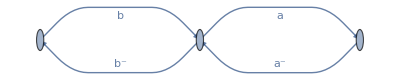

```mathematica
PlotQuiver[Q]
```

Given a quiver and a polynomial f, we can compute the set of signatures of f. The corresponding function to do this is called “QSignature” and can be called with a single polynomial...

```mathematica
f = a**b**SuperMinus[b]**SuperMinus[a]**a**b-a**b;
QSignature[f,Q]
```

{{U,W}}

...or with a list of polynomials

```mathematica
g =  b**SuperMinus[b]**b**SuperMinus[b]+ 1;
QSignature[{f,g},Q]
```

{{{U,W}},{{V,V}}}

The result of this function is the signature of each of the input polynomials given as a list of pairs. If the signature of a polynomial f is non-empty, f is compatible with the corresponding quiver. A stronger notion of compatibility is uniform compatibility. Both, compatibility as well as uniform compatibility of a polynomial with a quiver, can be tested explicitly using the functions  “CompatibleQ” and “UniformlyCompatibleQ”, respectively, which return True in the affirmative case and False otherwise.

```mathematica
CompatibleQ[f,Q]
UniformlyCompatibleQ[f,Q]
```

True

True

```mathematica
CompatibleQ[g,Q]
UniformlyCompatibleQ[g,Q]
```

True

False

### Quivers with non-unique labels

All functionality described in this section is also available for quiver with non-unique labels. Hence, we can also set up a quiver as follows:

```mathematica
Q2={{a,V,W},{SuperMinus[a],W,V},{b,U,V},{SuperMinus[b],V,U},{a,X,W}};
```

This yields a quiver where two different edges are labelled with a.

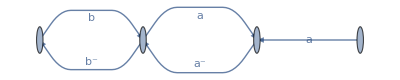

```mathematica
PlotQuiver[Q2]
```

As before, we can also compute the set of signatures of different polynomials with respect to Q2 ...

```mathematica
f = a**SuperMinus[a]**a - a;
g =  b**SuperMinus[b]**b**SuperMinus[b]+ 1;
QSignature[f,Q2]
QSignature[g,Q2]
```

{{V,W},{X,W}}

{{V,V}}

...  and check whether they are (uniformly) compatible with Q2.

```mathematica
CompatibleQ[{f,g},Q2]
UniformlyCompatibleQ[{f,g},Q2]
```

True

False

## Certify for the advanced user

In the first section, we have described the basic use of the “Certify” command, which provides a simple and fast way to  automatically prove operator identities. In this section, we present some additional parameters that can be set when calling “Certify” in order to obtain more information or speed up the computation.

In fact, the full syntax of the Certify command is

Certify[assumptions, claim, Q, MaxIter->10, MaxDeg->Infinity, MultiLex->False, Parallel->True, Sorted->True, Criterion->True],

where the arguments “assumptions”, “claim” and “Q” are mandatory and have already been discussed. We note that “claim” does not necessarily have to be only a single polynomial. In fact, “claim” can also be a list of polynomials. We illustrate this on the example presented in the first section, where we add a second claim f_2.

```mathematica
assumptions = {a**SuperMinus[a]**a-a,b**SuperMinus[b]**b-b,SuperMinus[a]**a**b**SuperMinus[b]**SuperMinus[a]**a**b**SuperMinus[b]-SuperMinus[a]**a**b**SuperMinus[b]};
Q={{a,V,W},{SuperMinus[a],W,V},{b,U,V},{SuperMinus[b],V,U}};
Subscript[f, 1]= a**b**SuperMinus[b]**SuperMinus[a]**a**b-a**b;
Subscript[f, 2] = -SuperMinus[a]**a**b+SuperMinus[a]**a**b**SuperMinus[b]**SuperMinus[a]**a**b;
result = Certify[assumptions,{Subscript[f, 1],Subscript[f, 2]},Q]
```

Done! All claims were successfully reduced to 0.

{{{a,-b+b**b^-**b,1},{-a**b**b^-**a^-**a,-b+b**b^-**b,1},{a,-a^-**a**b**b^-+a^-**a**b**b^-**a^-**a**b**b^-,b},{-1,-a+a**a^-**a,b**b^-**a^-**a**b**b^-**b},{1,-a+a**a^-**a,b**b^-**b}},{{a^-**a,-b+b**b^-**b,1},{-a^-**a**b**b^-**a^-**a,-b+b**b^-**b,1},{1,-a^-**a**b**b^-+a^-**a**b**b^-**a^-**a**b**b^-,b}}}

Now, the output is a list of lists of triples, where the i-th entry forms a linear combination of the i-th entry of “claim”.

```mathematica
MultiplyOut[result[[1]]] === Subscript[f, 1]
MultiplyOut[result[[2]]] === Subscript[f, 2]
```

True

True

Internally, “Certify” first checks whether all assumptions are uniformly compatible and all claims are compatible with the input quiver Q, then it computes a (partial) Groebner basis of the ideal generated by the assumptions and tries to verify the ideal membership of the claims in this ideal. Finally, it rewrites the linear combinations that it obtained during this Groebner basis and reduction computations and returns them.

If one of these steps fail, in particular, if only one step fails for a single polynomial contained in “claim”, the program returns $Failed.

```mathematica
Certify[assumptions,{Subscript[f, 1]+a**b,Subscript[f, 2]},Q]
```

Failed! Not all claims could be reduced to 0.

$Failed

To receive more information about the computation and the output, the global variable “VerboseOperatorGB” can be set to some positive integer. By default this value is set to 0. If it is set to a positive integer, this then also prints some information about the computational progress and gives a more detailed output.

If “VerboseOperatorGB” is set to 0, no information about the internal computations is given and the output is either a linear combination of the claim(s)in terms of the assumptions or $Failed (as discussed in the first section).

If “VerboseOperatorGB” is set to a positive integer, detailed information about the computational progress is given (the higher the value of “VerboseOperatorGB”, the more detailed the information that is printed). Additionally, if “VerboseOperatorGB” is set to a positive value, the output is of the form {S_A,S_C,red, linearComb}, where S_A is a list containing the signatures of each element in “assumptions” with respect to Q,  S_C is a list containing the signatures of each element in “claim” with respect to Q, “red” is a list {f_1', ... , f_n'} containing a normal form f_i' of each element f_i in “claim” with respect to a (partial) Groebner basis and “linearComb” is a list of linear combinations such that the i-th entry of “linearComb” forms a linear combination of f_i- f_i'.

```mathematica
VerboseOperatorGB = 1;
result = Certify[assumptions,{Subscript[f, 1],Subscript[f, 2]},Q]
```

Using the following monomial ordering:

a < a^- < b < b^-

Interreduced the input from 3 polynomials to 3.

Computing a (partial) Groebner basis and reducing the claim...

G has 3 elements in the beginning.

Starting iteration 1...

5 ambiguities in total

Iteration 1 finished. G has now 5 elements

G has 5 elements in the beginning.

Starting iteration 2...

15 ambiguities in total

Iteration 2 finished. G has now 6 elements

Done! All claims were successfully reduced to 0.

{{{{V,W}},{{U,V}},{{V,V}}},{{{U,W}},{{U,V}}},{0,0},{{{a,-b+b**b^-**b,1},{-a**b**b^-**a^-**a,-b+b**b^-**b,1},{a,-a^-**a**b**b^-+a^-**a**b**b^-**a^-**a**b**b^-,b},{-1,-a+a**a^-**a,b**b^-**a^-**a**b**b^-**b},{1,-a+a**a^-**a,b**b^-**b}},{{a^-**a,-b+b**b^-**b,1},{-a^-**a**b**b^-**a^-**a,-b+b**b^-**b,1},{1,-a^-**a**b**b^-+a^-**a**b**b^-**a^-**a**b**b^-,b}}}}

It follows from

```mathematica
result[[3]]
```

{0,0}

that both claims could be reduced to zero by a (partial) Groebner basis. Additionally, result[[4]] contains as its first element a linear combination of f_1in terms of the elements in “assumptions” and as its second element a linear combination of f_2in terms of the elements in “assumptions”.

```mathematica
MultiplyOut[result[[4,1]]] === Subscript[f, 1]
MultiplyOut[result[[4,2]]] === Subscript[f, 2]
```

True

True

Note that if “VerboseOperatorGB” is set to a positive value and a claim cannot be reduced to zero, we do not obtain $Failed but the (non-zero) normal form.

```mathematica
Certify[assumptions,Subscript[f, 1]+ a**b,Q]
```

Using the following monomial ordering:

a < a^- < b < b^-

Interreduced the input from 3 polynomials to 3.

Computing a (partial) Groebner basis and reducing the claim...

G has 3 elements in the beginning.

Starting iteration 1...

5 ambiguities in total

Iteration 1 finished. G has now 5 elements

G has 5 elements in the beginning.

Starting iteration 2...

15 ambiguities in total

Iteration 2 finished. G has now 6 elements

G has 6 elements in the beginning.

Starting iteration 3...

12 ambiguities in total

Iteration 3 finished. G has now 6 elements

G has 6 elements in the beginning.

Starting iteration 4...

5 ambiguities in total

Iteration 4 finished. G has now 6 elements

G has 6 elements in the beginning.

Starting iteration 5...

5 ambiguities in total

Iteration 5 finished. G has now 6 elements

G has 6 elements in the beginning.

Starting iteration 6...

5 ambiguities in total

Iteration 6 finished. G has now 6 elements

G has 6 elements in the beginning.

Starting iteration 7...

5 ambiguities in total

Iteration 7 finished. G has now 6 elements

G has 6 elements in the beginning.

Starting iteration 8...

5 ambiguities in total

Iteration 8 finished. G has now 6 elements

G has 6 elements in the beginning.

Starting iteration 9...

5 ambiguities in total

Iteration 9 finished. G has now 6 elements

G has 6 elements in the beginning.

Starting iteration 10...

5 ambiguities in total

Iteration 10 finished. G has now 6 elements

Failed! Not all claims could be reduced to 0.

{{{{V,W}},{{U,V}},{{V,V}}},{{U,W}},a**b,{{a,-b+b**b^-**b,1},{-a**b**b^-**a^-**a,-b+b**b^-**b,1},{a,-a^-**a**b**b^-+a^-**a**b**b^-**a^-**a**b**b^-,b},{-1,-a+a**a^-**a,b**b^-**a^-**a**b**b^-**b},{1,-a+a**a^-**a,b**b^-**b}}}

The optional arguments “MaxIter” (default: 10), “MaxDeg” (default: Infinity), “Parallel” (default: True), “Sorted” (default: True) and “Criterion” (default: True) are the same as for the “Groebner” method (see subsection “Additional information” at the end of “Certifying ideal membership”).

The final optional parameter “MultiLex” (default: False) determines whether a degree lexicographic (default) or a multigraded lexicographic order is used to compute the (partial) Groebner basis. If “MultiLex” is set to True, a multigraded order is used, where the first block of variables contains all indeterminates that appear in “claim” and the second block consists of the remaining variables. Setting “MultiLex” to True might speed up the computation.

```mathematica
VerboseOperatorGB = 0;
```

## Useful auxiliary functions

The package also provides some auxiliary functions which shall make the life of the user a bit easier when it comes to entering the polynomials for the Groebner/Certify command. In particular, we provide functionality to easily work with adjoint operators, a function to automatically generate the 4 defining identities of the Moore-Penrose inverse and a function to generate the trivial quiver for a given set of polynomials.

#### Adjoint operator

In many operator identities the adjoint operator A^* of an operator A appears. Our package provides some functionality to work with these adjoint operators, such as automatically expanding the adjoint of products or sums. To this end, an adjoint operator A^* has to be translated to adj[a]. Also products like (A B)^* can directly be translated to adj[a**b] and the package then expands this product automatically. Similarly, sums can be entered as adj[a+b], which then gets automatically processed to adj[a] + adj[b].

```mathematica
adj[a**b]
```

adj[b]**adj[a]

```mathematica
adj[2**a + a**b**c]
```

adj[a]**2+adj[c]**adj[b]**adj[a]

Furthermore, when an equation holds, then also the adjoint equation holds. So, when we have assumptions involving adjoint operators we often have to add the adjoint statements to our assumptions.  This process can be quite tedious when this has to be done by hand. So, we provide a function named AddAdj[F] that takes a set of polynomials F and returns a set containing F and all adjoint statements of F.

```mathematica
PinvA = {-a+a**SuperDagger[a]**a,SuperDagger[a]**a**SuperDagger[a]-SuperDagger[a],-a**SuperDagger[a]+adj[SuperDagger[a]]**adj[a],adj[a]**adj[SuperDagger[a]]-SuperDagger[a]**a};
```

```mathematica
assumptions = AddAdj[PinvA]
```

{-a+a**a^†**a,a^†**a**a^†-a^†,-a**a^†+adj[a^†]**adj[a],adj[a]**adj[a^†]-a^†**a,-adj[a]+adj[a]**adj[a^†]**adj[a],-adj[a^†]+adj[a^†]**adj[a]**adj[a^†],a**a^†-adj[a^†]**adj[a],-adj[a]**adj[a^†]+a^†**a}

#### Moore-Penrose identities

Often, we have to translate operator identities that involve the Moore-Penrose inverse A^† of an operator A. To quickly generate all 4 defining equations of A^† we provide the function Pinv[a] that takes a variable a and returns the 4 defining equations for the Moore-Penrose inverse of a. In this case, a new variable for the Moore-Penrose inverse will be introduced, namely a^†.

```mathematica
Pinv[a]
```

{-a+a**a^†**a,a^†**a**a^†-a^†,-a**a^†+adj[a^†]**adj[a],adj[a]**adj[a^†]-a^†**a}

```mathematica
Pinv[b]
```

{-b+b**b^†**b,b^†**b**b^†-b^†,-b**b^†+adj[b^†]**adj[b],adj[b]**adj[b^†]-b^†**b}

In some identities also the Moore-Penrose inverse of a product A B  appears. When we translate such an operator equation, we of course have to provide the 4 defining equations for (A B)^† but we also have to introduce a new variable for  the whole product (A B)^†. And in this case, we explicitly have to provide the name for this new variable by passing a second argument to Pinv. For example, by calling Pinv[a**b, a a b b], we obtain the 4 defining Moore-Penrose equations for (a b)^† and a new variable named a a b b will be introduced to denote (a b)^†.

```mathematica
Pinv[a**b,aabb]
```

{-a**b+a**b**aabb**a**b,-aabb+aabb**a**b**aabb,-a**b**aabb+adj[aabb]**adj[b]**adj[a],-aabb**a**b+adj[b]**adj[a]**adj[aabb]}

Only calling Pinv[a**b] can cause problems in further computations!

#### Trivial quiver

Often, we want to use the Certify command to quickly check whether a given set of assumptions implies some claims, without worrying about setting up a “correct” quiver that really captures all information about the domains and codomains of the operators involved. In this case, we can quickly set up a trivial quiver with which all polynomials are (uniformly) compatible. To this end, we provide the function TrivialQuiver[F], that takes a list of polynomials F and outputs a trivial quiver whose labels contain all variables appearing in the polynomials in F. Typically, this set F consists of all our assumptions and all claims.

```mathematica
assumptions = {a**b+c**adj[d],a**ab**c**d};
claims = {c**d**a**ab-b**c**SuperDagger[a]};
```

```mathematica
Q = TrivialQuiver[Join[assumptions,claims]]
```

{{a,1,1},{b,1,1},{c,1,1},{adj[d],1,1},{ab,1,1},{d,1,1},{a^†,1,1}}

## New since version 1.3

### Ideal exploration

```mathematica
SetUpRing[{x,y,z}]
```

Since version 1.3, the package also supports several functions to explore noncommutative ideals. This functionality allows the user to search in one- or two-sided ideals for polynomials of certain forms. In particular, the package provides the following methods.
	- Intersect[I,J, MaxIter→ 1]: intersects the two-sided ideals I and J. The optional argument “MaxIter” determines the maximal number of iterations of the underlying Gröbner basis computation (default: 1).

```mathematica
(* Intersection of two-sided ideals *)
I1 = {x**y};
I2= {y**z};
Intersect[I1,I2,MaxIter->3]
```

{x**y**z,y**z**x**y,x**y**y**z,-y**z**x**x**y,-y**z**y**x**y,-y**z**z**x**y,x**y**y**y**z}

- IntersectSubalgebra[I,S, MaxIter→ 5]: intersects the two-sided ideal I with the subalgebra S. The optional argument “MaxIter” determines the maximal number of iterations of the underlying Gröbner basis computation (default: 5).

```mathematica
(* Intersection of two-sided ideal with subalgebra *)
I1 = {x**x-3*x,x**y**x};
S = {x};
IntersectSubalgebra[I1,S,MaxIter->3]
```

{-3 x+x**x}

- IntersectRightIdeal[I,I_ρ,Q,MaxDeg→5]: intersects the two-sided ideal I with the right ideal I_ρ. Since a generating set of this intersection is typically very large/infinite, we restrict the output only to polynomials with are compatible with the quiver Q. The optional argument “MaxDeg” determines an upper bound on the lengths of the monomial that are considered during the computation, and hence, provides a stopping criterion (default: 5).

```mathematica
(* Intersection of two-sided ideal with right ideal *)
I1 = {x**y};
Subscript[I2, ρ] = {x,z};
(* First, we want to find all elements in the intersection I1 ∩ Subscript[I2, ρ] *)
(* In this case, we can set Q to be the trivial quiver over all variables that appear in our ideals. We also set the Length bound to 3 *)
Q = TrivialQuiver[{x,y,z}];
IntersectRightIdeal[I1,Subscript[I2, ρ],Q,MaxDeg->3]
```

{x**y,x**x**y,z**x**y,x**x**x**y,x**z**x**y,z**x**x**y,z**y**x**y,z**z**x**y,x**x**x**x**y,x**x**z**x**y,x**z**x**x**y,x**z**y**x**y,x**z**z**x**y,z**x**x**x**y,z**x**z**x**y,z**y**x**x**y,z**y**y**x**y,z**y**z**x**y,z**z**x**x**y,z**z**y**x**y,z**z**z**x**y}

```mathematica
(* As can be seen, the number of generators of this intersection grows quite fast. So, we now want to restrict ourselves only to generators where the variable cannot appear to the left of x or y. This can be done by specifiying the following quiver *)
Q = {{x,1,1},{y,1,1},{z,2,1}};
IntersectRightIdeal[I1,Subscript[I2, ρ],Q,MaxDeg->3]
```

{x**y,x**x**y,x**x**x**y,x**x**x**x**y}

- IntersectLeftIdeal[I,I_λ,Q,MaxDeg→5]: intersects the two-sided ideal I with the left ideal I_λ. Since a generating set of this intersection is typically very large/infinite, we restrict the output only to polynomials with are compatible with the quiver Q. The optional argument “MaxDeg” determines an upper bound on the degree of the monomials that are considered during the computation, and hence, provides a stopping criterion (default: 5).

(We do not provide any examples here since the syntax is completely analogous to “IntersectRightIdeal” presented above.)

REMARK: Note that cofactor representations are not yet supported for these intersections.

- Hom[cofactors,I,maxiter,A:I_n]: computes a generating set of hom_A(I), the ideal generated by all polynomials in the two-sided ideal I that are homogeneous w.r.t. the degree specified by the matrix A. The i-th row in A specifies the degree of x_i, where the x_i are ordered as they appear in “WordOrder”. By default, A is the identity matrix I_n. Additionally, for each polynomial f in the output, a cofactor representation of f in terms of the generators of I is saved in “cofactors”.

```mathematica
(* Homogeneous part of two-sided ideal *)
I2 = {x**y-y,x+y**x,z**y**x};
cofactors = {};
Hom[cofactors,I2,3]
```

{z**x,z**y,-x**y**x+y**x**x,-x**y**y+y**x**y}

```mathematica
(* Homogeneous part with custom degree *)
(* Now we want to use a degree where deg(x) = 2 Subscript[e, 1], deg(y) = -Subscript[e, 1], deg(z) = Subscript[e, 2] *) 
cofactors = {};
Hom[cofactors,I2,3,{{2,0},{-1,0},{0,1}}]
```

{-x**y**y**x+y**x**y**x,z**y,-x**y**x+y**x**x,-x**y**y+y**x**y,-x+x**y**y**x,-y+x**y**y**y,z**x}

- Mon[cofactors, I, maxiter, OneSided → “right”]: computes a generating set of mon(I), the one-sided ideal generated by all monomials in the one-sided ideal I. Additionally, for each polynomial f in the output, a cofactor representation of f in terms of the generators of I is saved in “cofactors”. The argument “maxiter” determines an upper bound on the number of iterations of a Gröbner basis computation that is done during this procedure. The optional value “OneSided” determines whether I (and consequently also the output mon(I)) is considered as a right ideal or as a left ideal (default: “right”).

```mathematica
(* Monomial part of a right ideal *)
I1 = {x**x**y-y**x,x**x+x**y-x, x**y**x**y-y**x**y,x**y**x};
cofactors = {};
Mon[cofactors,I1,5]
```

{x**y**x,y**x**y,x**x**y**y,x**x**x**y**y}

```mathematica
(* Now, we consider I1 as a left ideal *)
cofactors = {};
Mon[cofactors,I1,5,OneSided->"left"]
```

{x**y**x}

As can be seen, some of these functions require the ideal to be one-sided. To this end, we also provide the methods ToRightGB[I,d,X,Q] and ToLeftGB[I,d,X,Q] that take a two-sided ideal I, a quiver Q, a set of variables X and an integer d as input and enumerate a right/left Gröbner basis of I. Since these Gröbner bases are typically infinite, the variable d gives an upper bound on the degree of the monomials that are considered during the computation, and thereby, provides a stopping criterion. 
Additionally, we restrict ourselves to only compute generators that are compatible with the quiver Q. This can drastically speed up the computation. The set X determines which variables may appear in the generators, i.e. the computations are done in ℚ⟨X⟩.

```mathematica
(* If we want to consider I1 as a two-sided ideal, we first have to translate the two-sided generating set into a one-sided generating set. In this example, we will translate it into a right generating set. *)
(* Since we do not want to restrict our computations in any way, we set Q to be the trivial quiver and X is the set of all variables that appear in our ideal *)
X= {x,y};
Q = TrivialQuiver[X];
OneSidedGeneratingSet =ToRightGB[ I1,3,X,Q];
cofactors = {};
Mon[cofactors,OneSidedGeneratingSet,4]
```

{y**x,x**y**x}

### Module Gröbner bases

The package also supports the computation of Module Gröbner bases, this includes left/right modules as well as bimodules. One should note that left/right module Gröbner bases can also be computed by the regular Gröbner basis algorithm where the module basis elements are just considered as additional variables. For bimodules, however, this does not hold. Bimodule Gröbner bases can only be computed using the method “ModuleGroebner”, which has exactly the same input arguments and optional inputs as the regular “Groebner” method with the only exception that instead of an ideal this method takes a generating set of a (sub-)module as input.

In order to use this method, the basis of the considered module has to be specified. Note that the order of the basis elements matters. The module term ordering will be based on the ordering of the basis elements given here. In this example, we have e_1< e_2 < e_3. Additionally, also a monomial ordering has to be specified using the “SetUpRing” method (exactly as in the case of regular Gröbner basis computations).

```mathematica
SetModuleBasis[{Subscript[e, 1],Subscript[e, 2],Subscript[e, 3]}]
SetUpRing[{x,y,z}]
M = {y**x**Subscript[e, 2]**y-Subscript[e, 2],Subscript[e, 2]**y**y+x**Subscript[e, 1]};
G = ModuleGroebner[cofactors,M,3]
```

{y**x**e_2**y-e_2,x**e_1+e_2**y**y,e_2**y+y**x**x**e_1}

As in the case of regular Gröbner basis computations, we save a list of cofactor representations in the list “cofactors”.

```mathematica
cofactors
```

{{{1,y**x**e_2**y-e_2,1}},{{1,x**e_1+e_2**y**y,1}},{{-1,y**x**e_2**y-e_2,y},{y**x,x**e_1+e_2**y**y,1}}}

```mathematica
cofactors[[3]]
(cofactors[[3]]//MultiplyOut) ===G[[3]]
```

{{-1,y**x**e_2**y-e_2,y},{y**x,x**e_1+e_2**y**y,1}}

True

### Cancellability

The package now also supports easy-to-use interfaces to apply different properties of operators. One such property is what we call (left and right) cancellability. We say that an operator A B is left cancellable if for all operators C
								A B C = 0 ⇒  B C= 0.
Similarly, an operator B C is right cancellable if for all operators A
								A B C = 0 ⇒ A B = 0.
For example, *-cancellable operators are cancellable, injective operators are left cancellable, and surjective operators are right cancellable.

In terms of polynomials, we can translate the statement of A B being left cancellable into
									a b c ∈ I  ⇒ b c ∈ I.
Similarly, B C being right cancellability translates into
									a b c ∈ I  ⇒ a b ∈ I.

Hence, if we know that A B is left cancellable, then we can search in the ideal for elements of the form a b c and if we find some, add the corresponding part b c to the ideal. This is exactly what the methods “ApplyLeftCancellability” and “ApplyRightCancellability” allow the user to do.

In the following, we only discuss “ApplyLeftCancellability”. The syntax for “ApplyRightCancellability” is analogous. “ApplyLeftCancellability” takes a two-sided ideal I, an expression a b, the subexpression b and the optional arguments “MaxIter”, “Algorithm”, and “Vars” as input. It return elements of the form b c such that a b c ∈ I. The optional argument “MaxIter” determines how many iterations of the underlying Gröbner basis computation are executed (default: 1). The optional argument “Algorithm” determines which algorithm is used to search for the elements a b c ∈ I. The user can choose between “two-sided” (in this case, the intersection of the two two-sided ideals I and (a b) is computed), “one-sided” (in this case, the intersection between the two-sided ideal I and the right ideal (a b) is computed) and “subalgebra” (in this case, the intersection between the two-sided ideal I and the subalgebra generated by a b and all variables in the Vars is computed).   The default value for “Algorithm” is “subalgebra”.
The optional argument “Vars” is a set of variables, i.e. a subset of WordOrder, and determines in which noncommutative polynomial ring the computations are done (default: Vars = WordOrder).

To illustrate the usage of this function, we show that the composition of two linear injective operators A and B is  injective. To this end, we have to show that A B X = 0 ⇒ X = 0 for any operator X, or in terms of polynomials a b x ∈ I ⇒ x∈ I. To exploit the injectivity of A and B, we can simply use the method “ApplyLeftCancellability”. First, we apply this function to a and whenever we find an expression of the form a y, we add y to our assumptions. Then, we do the same thing for b. After doing these steps, we can see that x has been added to our assumptions, which proves our statement.

```mathematica
SetUpRing[{a,b,x}]
assumptions = {a**b**x};
injA = ApplyLeftCancellability[assumptions,a,a,MaxIter->3,Algorithm->"one-sided"];
assumptions = Join[assumptions,injA];
injB = ApplyLeftCancellability[assumptions,b,b,MaxIter->3,Algorithm->"one-sided"];
assumptions = Join[assumptions,injB]
```

{a**b**x,b**x,x}

### Diagram chasing

Similarly to the interface for cancellability, we also provide a simple-to-use interface to do diagram chasing proofs. To this end, we provide the function “DiagramChase” that takes as input an ideal I and a integer i. The ideal I should be generated by polynomials describing some diagram for which a proof by diagram chasing shall be found. Addtionally, the user can also provide the optional arguments “ExactAt”, “Mono”, “Epi”, “Algorithm”, and “MaxIter”. “ExactAt” is a list of pairs of variables determining which sequences in the diagram are exact. Similarly, “Mono” and “Epi” are lists of variables that determine which morphism in the diagram are monomorphism and epimorphism, respectively. By default, “ExactAt”, “Mono” and “”Epi” are all empty. The optional argument “Algorithm” determines which algorithm is used for the underlying computations. The options here are “one-sided”, “two-sided” and “subalgebra” (default: “one-sided”). See the section on “Cancellability” for more information about these algorithms. The optional argument “MaxIter” determines how many iterations of the underlying Gröbner basis computations are executed (default: 3).

The method takes the ideal I and performs a total of i iterations of the following steps:
	- Apply the property of m being a monomorphism for all m ∈ Mono in order to enlarge I,
	-  Apply the property of e being an epimorphism for all e ∈ Epi in order to enlarge I,
	- Apply the property of (a,b) being exact for all (a,b)∈ ExactAt in order to enlarge I,
	- Compute a (partial) Gröbner basis of I
Finally, the method returns a (partial) Gröbner basis of the enlarged ideal I.

We illustrate the usage of this function, on the following statement. Note that we name our variables by the same letters as the morphism in the diagram.

Consider the commutative diagram with exact rows
A   →^f       B    →^g     C    →^h    D 
α↓          β↓            γ↓         δ↓
A’   →^f'    B’   →^g'   C’  →^h'   D’
If β and δ are mono and α is epi, then γ is epi.

Hence, we have to show that 
	γc = 0     ⇒     c = 0,		or in terms of polynomials   γc ∈ I    ⇒     c ∈ I
for arbitrary c. We note that since epimorphism are right cancellable, it suffices to show that c e ∈ I for some epimorphism e.

First, we have to encode the properties of this diagram being commutative and the exactness of the rows in terms of polynomials. If a sequence A   →^f       B    →^g     C  is exact, we have to add the polynomial g f to our assumptions.
We can also assume that γ c ∈ I. These polynomials form our assumptions.

```mathematica
ClearAll[f,g,h]
commutativity = {β**f-f'**α,γ**g-g'**β,δ**h-h'**γ};
exactness ={g**f,h**g,g'**f',h'**g'};
mono = {γ**c};
assumptions = Join[commutativity,exactness,mono];
```

Next, we have to provide a monomial ordering. We choose the following multilex ordering.

```mathematica
SetUpRing[{c},{f,g,h,f',g',h'},{α,β,γ,δ}]
```

Then, we only have to call the method “DiagramChase”, where we specify our exactness assumptions and the assumptions about certain morphisms being mono or epi.

```mathematica
G = DiagramChase[assumptions,3,ExactAt->{{f,g},{g,h},{f',g'},{g',h'}},Mono->{β,δ},Epi->{α}]
```

Starting iteration 1...

Starting iteration 2...

Starting iteration 3...

{β**f-f'**α,γ**g-g'**β,δ**h-h'**γ,g**f,h**g,g'**f',h'**g',γ**c,h**c,-c**e2374+g**y2375,-f'**y2388+β**f**e2386,-f'**y2389+β**y2375**e2387,-g'**y2402+γ**c**e2400,-g'**y2403+γ**g**e2401,g'**β**y2375,-f'**y2388+f'**α**e2386,g'**y2402,-g'**y2403+g'**β**e2401,y2388**e2453-α**y2451,y2389**e2454-α**y2452,y2402**e2589-f'**y2591,-y2403**e2590-f'**y2592+β**e2401**e2590,-f**y2451+f**e2386**e2453,-f**y2452+y2375**e2387**e2454,y2591**e2637-α**y2635,y2592**e2638-α**y2636,-f**y2806+y2375**e2387**e2454**e2805,c**e2374**e2387**e2454,-f**y2806+f**y2452**e2805,-f'**α**y2806+f'**α**y2452**e2805}

Note that “DiagramChase” introduces new variables. Each variable starting with a y stands for an arbitrary morphism and each variable starting with an e stands for an epimorphism. As already remarked above, it suffices to show that c e ∈ I for some epimorphism e. And indeed we have...

```mathematica
Cases[G,c**___]
```

{c**e2374**e2387**e2454}